```mathematica
ClearAll[line, files, importfile, raw, dataset, dataset1WithErrs]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/data.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/~$data.xlsx}

```mathematica
importfile = files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/data.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

## Dataset

```mathematica
dataset=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset[All,<|"n"->(#n&),"T"->(Around[#T,#dt]&)|>]
```

Dataset[<>]

```mathematica
line =LinearModelFit[Normal@dataset[All,{"n","T"}/*Values],{1,x},x]
```

FittedModel[0.00692389+0.212328 x]

```mathematica
line["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00692389 | 0.0125521 | 0.55161 | 0.586775
x | 0.212328 | 0.00165773 | 128.084 | 4.18263×10^-33

```mathematica
Normal@line
```

0.00692389+0.212328 x

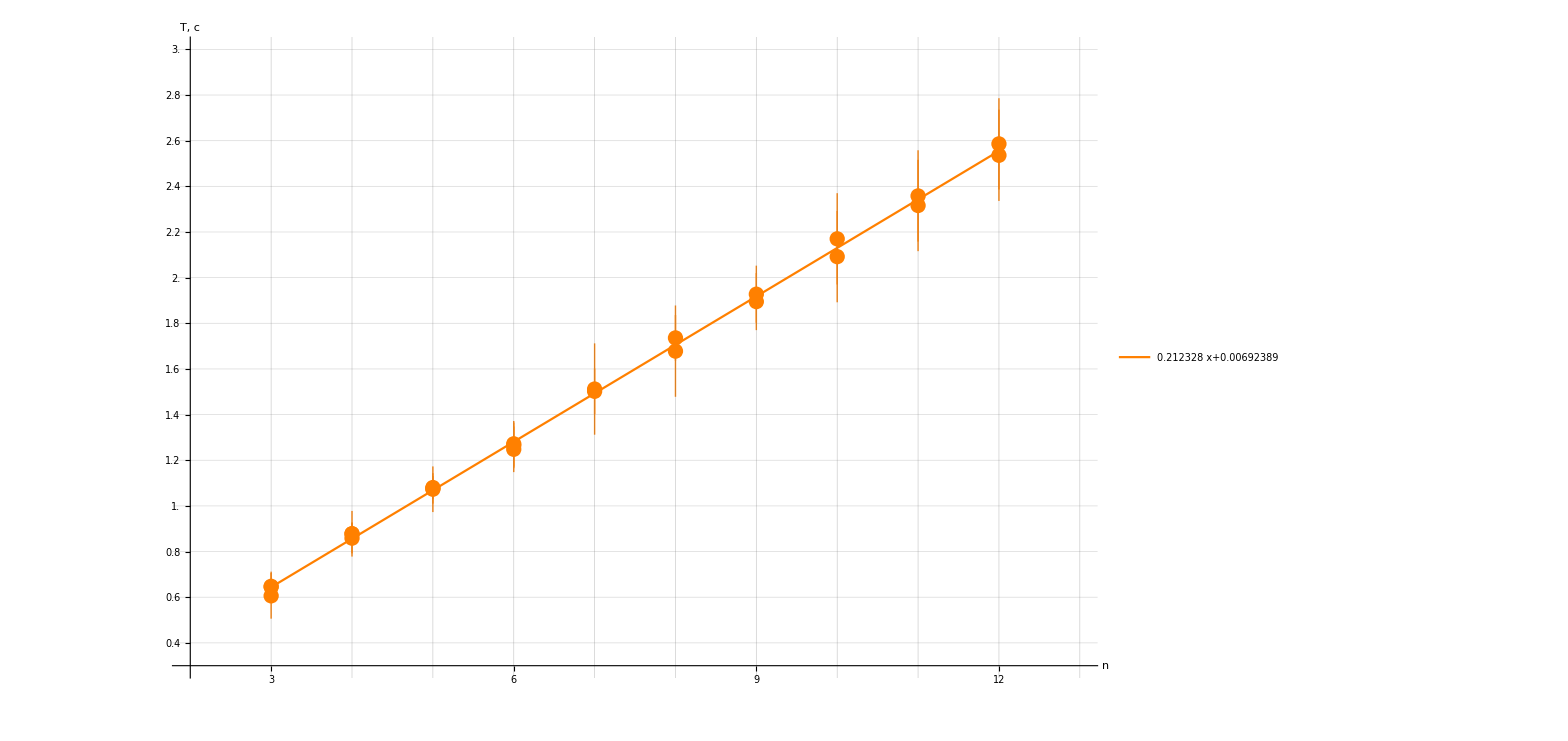

```mathematica
Show[
Plot[
{line@x},
{x,3, 12},
AxesLabel->{Style["n", Large],Style["T, c",Large]},
ImageSize->1200,
AxesStyle->Directive[Arrowheads[{0.02}],Black],
GridLines-> {Range[0,15,1],Range[0,10,0.1]},
PlotRange->{{2,13},{0.3,3.}},
Ticks-> {Range[0,50,1],Range[0,3,0.2]},
TicksStyle->15,
PlotStyle->Orange,
PlotLegends->Placed[
LineLegend[
{Normal@line},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
]
],
ListPlot[
{dataset1WithErrs},
PlotStyle->Orange
]
]
```

```mathematica
ClearAll[line, files, importfile, raw, dataset, dataset1WithErrs]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/data2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/data.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/~$data2.xlsx}

```mathematica
importfile = files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/data2.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
dataset2=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"n"->(#n&),"M"->(Around[#M,#dm]&)|>]
```

Dataset[<>]

```mathematica
line2 =LinearModelFit[Normal@dataset2[All,{"n","M"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+37.7518 x]

```mathematica
line2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 37.7518 | 2.0908 | 18.0561 | 0.00305322

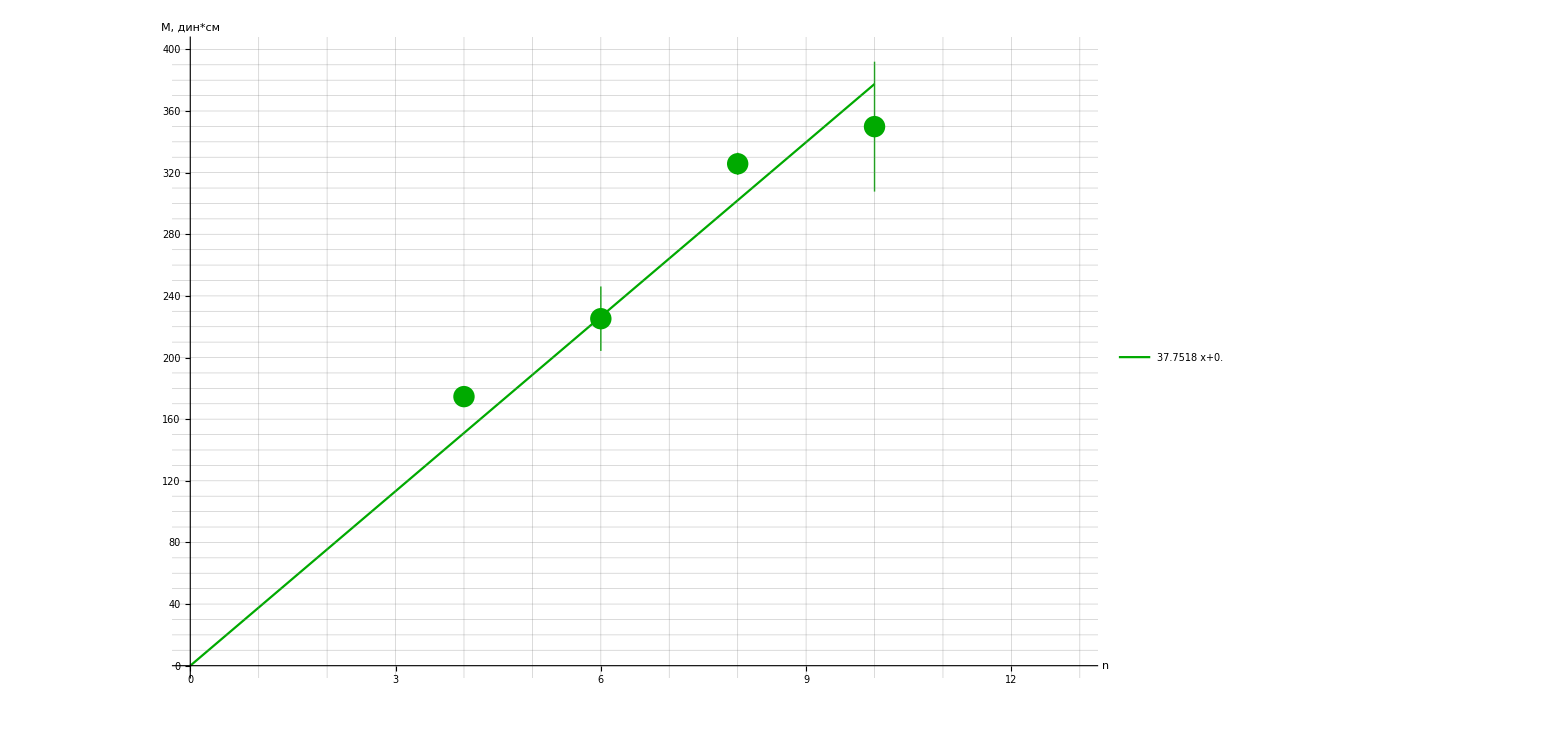

```mathematica
Show[
Plot[
{line2@x},
{x,0, 10},
AxesLabel->{Style["n", Large],Style["M, дин*см",Large]},
ImageSize->1200,
AxesStyle->Directive[Arrowheads[{0.02}],Black],
GridLines-> {Range[0,15,1],Range[0,400,10]},
PlotRange->{{0,13},{0,400}},
Ticks-> {Range[0,50,1],Range[0,400,20]},
TicksStyle->15,
PlotStyle->Darker[Green],
PlotLegends->Placed[
LineLegend[
{Normal@line2},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
]
],
ListPlot[
{dataset2WithErrs},
PlotStyle->Darker[Green]
]
]
```